```mathematica
(*Article: The Role of Direct Capital Cash Transfers Towards Poverty and Extreme Poverty Alleviation - An Omega Risk Process*)
                                                      (*Authors: Flores-Contró, José M. and Arnold, Séverine*)
```

```mathematica
(*We first clean our environment.*)
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
(*Now, we calculate the value of the constants as explained in Appendix A.4.*)
```

```mathematica
Subscript[m, l][x_]:=1+A2(x/B)^(1-c+1-α)Hypergeometric2F1[a-c+1,b-c+1,2-c,x/B]
```

```mathematica
Subscript[m, m][x_]:=A3(-x/((B CT- r χ)/(r-CT)))^-d Hypergeometric2F1[d,d-f+1,d-e+1,(-x/((B CT- r χ)/(r-CT)))^-1]+A4(-x/((B CT- r χ)/(r-CT)))^-e Hypergeometric2F1[e,e-f+1,e-d+1,(-x/((B CT- r χ)/(r-CT)))^-1]
```

```mathematica
Subscript[m, u][x_]:=A6(x/χ)^-h Hypergeometric2F1[h,h-i+1,h-g+1,(x/χ)^-1]
```

```mathematica
sol1:=FullSimplify[Solve[Subscript[m, l][χ]==Subscript[m, m][χ],A3]]
```

```mathematica
A3:=-(((((CT-r) χ)/(B CT-r χ))^d (-1-A2 (χ/B)^(2-c-α) Hypergeometric2F1[1+a-c,1+b-c,2-c,χ/B]+A4 (((CT-r) χ)/(B CT-r χ))^-e Hypergeometric2F1[e,1+e-f,1-d+e,(B CT-r χ)/(CT χ-r χ)]))/Hypergeometric2F1[d,1+d-f,1+d-e,(B CT-r χ)/(CT χ-r χ)])
```

```mathematica
Subscript[m, m][x_]:=A3(-x/((B CT- r χ)/(r-CT)))^-d Hypergeometric2F1[d,d-f+1,d-e+1,(-x/((B CT- r χ)/(r-CT)))^-1]+A4(-x/((B CT- r χ)/(r-CT)))^-e Hypergeometric2F1[e,e-f+1,e-d+1,(-x/((B CT- r χ)/(r-CT)))^-1]
```

```mathematica
sol2:=FullSimplify[Solve[Subscript[m, l]'[χ]==Subscript[m, m]'[χ],A2]]
```

```mathematica
A2:=(B^2 (χ/B)^(c+α) (((CT-r) χ)/(B CT-r χ))^-e (d Hypergeometric2F1[1+d,1+d-f,1+d-e,(B CT-r χ)/(CT χ-r χ)] ((((CT-r) χ)/(B CT-r χ))^e-A4 Hypergeometric2F1[e,1+e-f,1-d+e,(B CT-r χ)/(CT χ-r χ)])+A4 e Hypergeometric2F1[d,1+d-f,1+d-e,(B CT-r χ)/(CT χ-r χ)] Hypergeometric2F1[1+e,1+e-f,1-d+e,(B CT-r χ)/(CT χ-r χ)]))/(χ^2 Gamma[2-c] Gamma[1+d-e] ((-1-a+c) Hypergeometric2F1Regularized[2+a-c,1+b-c,2-c,χ/B] Hypergeometric2F1Regularized[d,1+d-f,1+d-e,(B CT-r χ)/(CT χ-r χ)]+Hypergeometric2F1Regularized[1+a-c,1+b-c,2-c,χ/B] ((-1+a+α) Hypergeometric2F1Regularized[d,1+d-f,1+d-e,(B CT-r χ)/(CT χ-r χ)]-d Hypergeometric2F1Regularized[1+d,1+d-f,1+d-e,(B CT-r χ)/(CT χ-r χ)])))
```

```mathematica
A3:=-(((((CT-r) χ)/(B CT-r χ))^d (-1-A2 (χ/B)^(2-c-α) Hypergeometric2F1[1+a-c,1+b-c,2-c,χ/B]+A4 (((CT-r) χ)/(B CT-r χ))^-e Hypergeometric2F1[e,1+e-f,1-d+e,(B CT-r χ)/(CT χ-r χ)]))/Hypergeometric2F1[d,1+d-f,1+d-e,(B CT-r χ)/(CT χ-r χ)])
```

```mathematica
Subscript[m, l][x_]:=1+A2(x/B)^(1-c+1-α)Hypergeometric2F1[a-c+1,b-c+1,2-c,x/B]
```

```mathematica
sol3:=FullSimplify[Solve[Subscript[m, m][B]==Subscript[m, u][B],A6]]
```

```mathematica
A6:=1/Hypergeometric2F1[h,1+h-i,1-g+h,χ/B](B/χ)^h (A4 ((B (CT-r))/(B CT-r χ))^-e Hypergeometric2F1[e,1+e-f,1-d+e,(B CT-r χ)/(B CT-B r)]+(((B (CT-r))/(B CT-r χ))^-d (((CT-r) χ)/(B CT-r χ))^(d-e) Hypergeometric2F1[d,1+d-f,1+d-e,(B CT-r χ)/(B CT-B r)] (-(1+a-c) Hypergeometric2F1[2+a-c,1+b-c,2-c,χ/B] ((((CT-r) χ)/(B CT-r χ))^e-A4 Hypergeometric2F1[e,1+e-f,1-d+e,(B CT-r χ)/(CT χ-r χ)])+Hypergeometric2F1[1+a-c,1+b-c,2-c,χ/B] ((-1+a+α) (((CT-r) χ)/(B CT-r χ))^e-A4 (-1+a+α) Hypergeometric2F1[e,1+e-f,1-d+e,(B CT-r χ)/(CT χ-r χ)]+A4 e Hypergeometric2F1[1+e,1+e-f,1-d+e,(B CT-r χ)/(CT χ-r χ)])))/(Gamma[2-c] Gamma[1+d-e] ((-1-a+c) Hypergeometric2F1Regularized[2+a-c,1+b-c,2-c,χ/B] Hypergeometric2F1Regularized[d,1+d-f,1+d-e,(B CT-r χ)/(CT χ-r χ)]+Hypergeometric2F1Regularized[1+a-c,1+b-c,2-c,χ/B] ((-1+a+α) Hypergeometric2F1Regularized[d,1+d-f,1+d-e,(B CT-r χ)/(CT χ-r χ)]-d Hypergeometric2F1Regularized[1+d,1+d-f,1+d-e,(B CT-r χ)/(CT χ-r χ)]))))
```

```mathematica
Subscript[m, u][x_]:=A6(x/χ)^-h Hypergeometric2F1[h,h-i+1,h-g+1,(x/χ)^-1]
```

```mathematica
sol4:=Solve[Subscript[m, m]'[B]==Subscript[m, u]'[B],A4]
```

```mathematica
A4:=(-(d (-CT+r) (-(B (-CT+r))/(B CT-r χ))^(-1-d) (((CT-r) χ)/(B CT-r χ))^d Hypergeometric2F1[d,1+d-f,1+d-e,-(B CT-r χ)/(B (-CT+r))])/((B CT-r χ) Hypergeometric2F1[d,1+d-f,1+d-e,(B CT-r χ)/(CT χ-r χ)])-(d (1+d-f) (-(B (-CT+r))/(B CT-r χ))^-d (((CT-r) χ)/(B CT-r χ))^d (B CT-r χ) Hypergeometric2F1[1+d,2+d-f,2+d-e,-(B CT-r χ)/(B (-CT+r))])/(B^2 (1+d-e) (-CT+r) Hypergeometric2F1[d,1+d-f,1+d-e,(B CT-r χ)/(CT χ-r χ)])-(h (-1+a+α) ((B (CT-r))/(B CT-r χ))^-d (((CT-r) χ)/(B CT-r χ))^d Hypergeometric2F1[1+a-c,1+b-c,2-c,χ/B] Hypergeometric2F1[d,1+d-f,1+d-e,(B CT-r χ)/(B CT-B r)])/(B Gamma[2-c] Gamma[1+d-e] ((-1-a+c) Hypergeometric2F1Regularized[2+a-c,1+b-c,2-c,χ/B] Hypergeometric2F1Regularized[d,1+d-f,1+d-e,(B CT-r χ)/(CT χ-r χ)]+Hypergeometric2F1Regularized[1+a-c,1+b-c,2-c,χ/B] ((-1+a+α) Hypergeometric2F1Regularized[d,1+d-f,1+d-e,(B CT-r χ)/(CT χ-r χ)]-d Hypergeometric2F1Regularized[1+d,1+d-f,1+d-e,(B CT-r χ)/(CT χ-r χ)])))-((-1-a+c) h ((B (CT-r))/(B CT-r χ))^-d (((CT-r) χ)/(B CT-r χ))^d Hypergeometric2F1[2+a-c,1+b-c,2-c,χ/B] Hypergeometric2F1[d,1+d-f,1+d-e,(B CT-r χ)/(B CT-B r)])/(B Gamma[2-c] Gamma[1+d-e] ((-1-a+c) Hypergeometric2F1Regularized[2+a-c,1+b-c,2-c,χ/B] Hypergeometric2F1Regularized[d,1+d-f,1+d-e,(B CT-r χ)/(CT χ-r χ)]+Hypergeometric2F1Regularized[1+a-c,1+b-c,2-c,χ/B] ((-1+a+α) Hypergeometric2F1Regularized[d,1+d-f,1+d-e,(B CT-r χ)/(CT χ-r χ)]-d Hypergeometric2F1Regularized[1+d,1+d-f,1+d-e,(B CT-r χ)/(CT χ-r χ)])))-(d^2 (-CT+r) (-(B (-CT+r))/(B CT-r χ))^(-1-d) (((CT-r) χ)/(B CT-r χ))^d Hypergeometric2F1[1+a-c,1+b-c,2-c,χ/B] Hypergeometric2F1[d,1+d-f,1+d-e,-(B CT-r χ)/(B (-CT+r))] Hypergeometric2F1[1+d,1+d-f,1+d-e,(B CT-r χ)/(CT χ-r χ)])/((B CT-r χ) Gamma[2-c] Gamma[1+d-e] Hypergeometric2F1[d,1+d-f,1+d-e,(B CT-r χ)/(CT χ-r χ)] ((-1-a+c) Hypergeometric2F1Regularized[2+a-c,1+b-c,2-c,χ/B] Hypergeometric2F1Regularized[d,1+d-f,1+d-e,(B CT-r χ)/(CT χ-r χ)]+Hypergeometric2F1Regularized[1+a-c,1+b-c,2-c,χ/B] ((-1+a+α) Hypergeometric2F1Regularized[d,1+d-f,1+d-e,(B CT-r χ)/(CT χ-r χ)]-d Hypergeometric2F1Regularized[1+d,1+d-f,1+d-e,(B CT-r χ)/(CT χ-r χ)])))-(d^2 (1+d-f) (-(B (-CT+r))/(B CT-r χ))^-d (((CT-r) χ)/(B CT-r χ))^d (B CT-r χ) Hypergeometric2F1[1+a-c,1+b-c,2-c,χ/B] Hypergeometric2F1[1+d,1+d-f,1+d-e,(B CT-r χ)/(CT χ-r χ)] Hypergeometric2F1[1+d,2+d-f,2+d-e,-(B CT-r χ)/(B (-CT+r))])/(B^2 (1+d-e) (-CT+r) Gamma[2-c] Gamma[1+d-e] Hypergeometric2F1[d,1+d-f,1+d-e,(B CT-r χ)/(CT χ-r χ)] ((-1-a+c) Hypergeometric2F1Regularized[2+a-c,1+b-c,2-c,χ/B] Hypergeometric2F1Regularized[d,1+d-f,1+d-e,(B CT-r χ)/(CT χ-r χ)]+Hypergeometric2F1Regularized[1+a-c,1+b-c,2-c,χ/B] ((-1+a+α) Hypergeometric2F1Regularized[d,1+d-f,1+d-e,(B CT-r χ)/(CT χ-r χ)]-d Hypergeometric2F1Regularized[1+d,1+d-f,1+d-e,(B CT-r χ)/(CT χ-r χ)])))-(h (1+h-i) (-1+a+α) χ ((B (CT-r))/(B CT-r χ))^-d (((CT-r) χ)/(B CT-r χ))^d Hypergeometric2F1[1+a-c,1+b-c,2-c,χ/B] Hypergeometric2F1[d,1+d-f,1+d-e,(B CT-r χ)/(B CT-B r)] Hypergeometric2F1[1+h,2+h-i,2-g+h,χ/B])/(B^2 (1-g+h) Gamma[2-c] Gamma[1+d-e] Hypergeometric2F1[h,1+h-i,1-g+h,χ/B] ((-1-a+c) Hypergeometric2F1Regularized[2+a-c,1+b-c,2-c,χ/B] Hypergeometric2F1Regularized[d,1+d-f,1+d-e,(B CT-r χ)/(CT χ-r χ)]+Hypergeometric2F1Regularized[1+a-c,1+b-c,2-c,χ/B] ((-1+a+α) Hypergeometric2F1Regularized[d,1+d-f,1+d-e,(B CT-r χ)/(CT χ-r χ)]-d Hypergeometric2F1Regularized[1+d,1+d-f,1+d-e,(B CT-r χ)/(CT χ-r χ)])))-((-1-a+c) h (1+h-i) χ ((B (CT-r))/(B CT-r χ))^-d (((CT-r) χ)/(B CT-r χ))^d Hypergeometric2F1[2+a-c,1+b-c,2-c,χ/B] Hypergeometric2F1[d,1+d-f,1+d-e,(B CT-r χ)/(B CT-B r)] Hypergeometric2F1[1+h,2+h-i,2-g+h,χ/B])/(B^2 (1-g+h) Gamma[2-c] Gamma[1+d-e] Hypergeometric2F1[h,1+h-i,1-g+h,χ/B] ((-1-a+c) Hypergeometric2F1Regularized[2+a-c,1+b-c,2-c,χ/B] Hypergeometric2F1Regularized[d,1+d-f,1+d-e,(B CT-r χ)/(CT χ-r χ)]+Hypergeometric2F1Regularized[1+a-c,1+b-c,2-c,χ/B] ((-1+a+α) Hypergeometric2F1Regularized[d,1+d-f,1+d-e,(B CT-r χ)/(CT χ-r χ)]-d Hypergeometric2F1Regularized[1+d,1+d-f,1+d-e,(B CT-r χ)/(CT χ-r χ)]))))/((e (-CT+r) (-(B (-CT+r))/(B CT-r χ))^(-1-e) Hypergeometric2F1[e,1+e-f,1-d+e,-(B CT-r χ)/(B (-CT+r))])/(B CT-r χ)+(h ((B (CT-r))/(B CT-r χ))^-e Hypergeometric2F1[e,1+e-f,1-d+e,(B CT-r χ)/(B CT-B r)])/B-(d (-CT+r) (-(B (-CT+r))/(B CT-r χ))^(-1-d) (((CT-r) χ)/(B CT-r χ))^(d-e) Hypergeometric2F1[d,1+d-f,1+d-e,-(B CT-r χ)/(B (-CT+r))] Hypergeometric2F1[e,1+e-f,1-d+e,(B CT-r χ)/(CT χ-r χ)])/((B CT-r χ) Hypergeometric2F1[d,1+d-f,1+d-e,(B CT-r χ)/(CT χ-r χ)])-(d (1+d-f) (-(B (-CT+r))/(B CT-r χ))^-d (((CT-r) χ)/(B CT-r χ))^(d-e) (B CT-r χ) Hypergeometric2F1[1+d,2+d-f,2+d-e,-(B CT-r χ)/(B (-CT+r))] Hypergeometric2F1[e,1+e-f,1-d+e,(B CT-r χ)/(CT χ-r χ)])/(B^2 (1+d-e) (-CT+r) Hypergeometric2F1[d,1+d-f,1+d-e,(B CT-r χ)/(CT χ-r χ)])+(e (1+e-f) (-(B (-CT+r))/(B CT-r χ))^-e (B CT-r χ) Hypergeometric2F1[1+e,2+e-f,2-d+e,-(B CT-r χ)/(B (-CT+r))])/(B^2 (1-d+e) (-CT+r))+(h (1+h-i) χ ((B (CT-r))/(B CT-r χ))^-e Hypergeometric2F1[e,1+e-f,1-d+e,(B CT-r χ)/(B CT-B r)] Hypergeometric2F1[1+h,2+h-i,2-g+h,χ/B])/(B^2 (1-g+h) Hypergeometric2F1[h,1+h-i,1-g+h,χ/B])-(h (-1+a+α) ((B (CT-r))/(B CT-r χ))^-d (((CT-r) χ)/(B CT-r χ))^(d-e) Hypergeometric2F1[1+a-c,1+b-c,2-c,χ/B] Hypergeometric2F1[d,1+d-f,1+d-e,(B CT-r χ)/(B CT-B r)] Hypergeometric2F1[e,1+e-f,1-d+e,(B CT-r χ)/(CT χ-r χ)])/(B Gamma[2-c] Gamma[1+d-e] ((-1-a+c) Hypergeometric2F1Regularized[2+a-c,1+b-c,2-c,χ/B] Hypergeometric2F1Regularized[d,1+d-f,1+d-e,(B CT-r χ)/(CT χ-r χ)]+Hypergeometric2F1Regularized[1+a-c,1+b-c,2-c,χ/B] ((-1+a+α) Hypergeometric2F1Regularized[d,1+d-f,1+d-e,(B CT-r χ)/(CT χ-r χ)]-d Hypergeometric2F1Regularized[1+d,1+d-f,1+d-e,(B CT-r χ)/(CT χ-r χ)])))-((-1-a+c) h ((B (CT-r))/(B CT-r χ))^-d (((CT-r) χ)/(B CT-r χ))^(d-e) Hypergeometric2F1[2+a-c,1+b-c,2-c,χ/B] Hypergeometric2F1[d,1+d-f,1+d-e,(B CT-r χ)/(B CT-B r)] Hypergeometric2F1[e,1+e-f,1-d+e,(B CT-r χ)/(CT χ-r χ)])/(B Gamma[2-c] Gamma[1+d-e] ((-1-a+c) Hypergeometric2F1Regularized[2+a-c,1+b-c,2-c,χ/B] Hypergeometric2F1Regularized[d,1+d-f,1+d-e,(B CT-r χ)/(CT χ-r χ)]+Hypergeometric2F1Regularized[1+a-c,1+b-c,2-c,χ/B] ((-1+a+α) Hypergeometric2F1Regularized[d,1+d-f,1+d-e,(B CT-r χ)/(CT χ-r χ)]-d Hypergeometric2F1Regularized[1+d,1+d-f,1+d-e,(B CT-r χ)/(CT χ-r χ)])))-(d^2 (-CT+r) (-(B (-CT+r))/(B CT-r χ))^(-1-d) (((CT-r) χ)/(B CT-r χ))^(d-e) Hypergeometric2F1[1+a-c,1+b-c,2-c,χ/B] Hypergeometric2F1[d,1+d-f,1+d-e,-(B CT-r χ)/(B (-CT+r))] Hypergeometric2F1[1+d,1+d-f,1+d-e,(B CT-r χ)/(CT χ-r χ)] Hypergeometric2F1[e,1+e-f,1-d+e,(B CT-r χ)/(CT χ-r χ)])/((B CT-r χ) Gamma[2-c] Gamma[1+d-e] Hypergeometric2F1[d,1+d-f,1+d-e,(B CT-r χ)/(CT χ-r χ)] ((-1-a+c) Hypergeometric2F1Regularized[2+a-c,1+b-c,2-c,χ/B] Hypergeometric2F1Regularized[d,1+d-f,1+d-e,(B CT-r χ)/(CT χ-r χ)]+Hypergeometric2F1Regularized[1+a-c,1+b-c,2-c,χ/B] ((-1+a+α) Hypergeometric2F1Regularized[d,1+d-f,1+d-e,(B CT-r χ)/(CT χ-r χ)]-d Hypergeometric2F1Regularized[1+d,1+d-f,1+d-e,(B CT-r χ)/(CT χ-r χ)])))-(d^2 (1+d-f) (-(B (-CT+r))/(B CT-r χ))^-d (((CT-r) χ)/(B CT-r χ))^(d-e) (B CT-r χ) Hypergeometric2F1[1+a-c,1+b-c,2-c,χ/B] Hypergeometric2F1[1+d,1+d-f,1+d-e,(B CT-r χ)/(CT χ-r χ)] Hypergeometric2F1[1+d,2+d-f,2+d-e,-(B CT-r χ)/(B (-CT+r))] Hypergeometric2F1[e,1+e-f,1-d+e,(B CT-r χ)/(CT χ-r χ)])/(B^2 (1+d-e) (-CT+r) Gamma[2-c] Gamma[1+d-e] Hypergeometric2F1[d,1+d-f,1+d-e,(B CT-r χ)/(CT χ-r χ)] ((-1-a+c) Hypergeometric2F1Regularized[2+a-c,1+b-c,2-c,χ/B] Hypergeometric2F1Regularized[d,1+d-f,1+d-e,(B CT-r χ)/(CT χ-r χ)]+Hypergeometric2F1Regularized[1+a-c,1+b-c,2-c,χ/B] ((-1+a+α) Hypergeometric2F1Regularized[d,1+d-f,1+d-e,(B CT-r χ)/(CT χ-r χ)]-d Hypergeometric2F1Regularized[1+d,1+d-f,1+d-e,(B CT-r χ)/(CT χ-r χ)])))+(d e (-CT+r) (-(B (-CT+r))/(B CT-r χ))^(-1-d) (((CT-r) χ)/(B CT-r χ))^(d-e) Hypergeometric2F1[1+a-c,1+b-c,2-c,χ/B] Hypergeometric2F1[d,1+d-f,1+d-e,-(B CT-r χ)/(B (-CT+r))] Hypergeometric2F1[1+e,1+e-f,1-d+e,(B CT-r χ)/(CT χ-r χ)])/((B CT-r χ) Gamma[2-c] Gamma[1+d-e] ((-1-a+c) Hypergeometric2F1Regularized[2+a-c,1+b-c,2-c,χ/B] Hypergeometric2F1Regularized[d,1+d-f,1+d-e,(B CT-r χ)/(CT χ-r χ)]+Hypergeometric2F1Regularized[1+a-c,1+b-c,2-c,χ/B] ((-1+a+α) Hypergeometric2F1Regularized[d,1+d-f,1+d-e,(B CT-r χ)/(CT χ-r χ)]-d Hypergeometric2F1Regularized[1+d,1+d-f,1+d-e,(B CT-r χ)/(CT χ-r χ)])))+(e h ((B (CT-r))/(B CT-r χ))^-d (((CT-r) χ)/(B CT-r χ))^(d-e) Hypergeometric2F1[1+a-c,1+b-c,2-c,χ/B] Hypergeometric2F1[d,1+d-f,1+d-e,(B CT-r χ)/(B CT-B r)] Hypergeometric2F1[1+e,1+e-f,1-d+e,(B CT-r χ)/(CT χ-r χ)])/(B Gamma[2-c] Gamma[1+d-e] ((-1-a+c) Hypergeometric2F1Regularized[2+a-c,1+b-c,2-c,χ/B] Hypergeometric2F1Regularized[d,1+d-f,1+d-e,(B CT-r χ)/(CT χ-r χ)]+Hypergeometric2F1Regularized[1+a-c,1+b-c,2-c,χ/B] ((-1+a+α) Hypergeometric2F1Regularized[d,1+d-f,1+d-e,(B CT-r χ)/(CT χ-r χ)]-d Hypergeometric2F1Regularized[1+d,1+d-f,1+d-e,(B CT-r χ)/(CT χ-r χ)])))+(d e (1+d-f) (-(B (-CT+r))/(B CT-r χ))^-d (((CT-r) χ)/(B CT-r χ))^(d-e) (B CT-r χ) Hypergeometric2F1[1+a-c,1+b-c,2-c,χ/B] Hypergeometric2F1[1+d,2+d-f,2+d-e,-(B CT-r χ)/(B (-CT+r))] Hypergeometric2F1[1+e,1+e-f,1-d+e,(B CT-r χ)/(CT χ-r χ)])/(B^2 (1+d-e) (-CT+r) Gamma[2-c] Gamma[1+d-e] ((-1-a+c) Hypergeometric2F1Regularized[2+a-c,1+b-c,2-c,χ/B] Hypergeometric2F1Regularized[d,1+d-f,1+d-e,(B CT-r χ)/(CT χ-r χ)]+Hypergeometric2F1Regularized[1+a-c,1+b-c,2-c,χ/B] ((-1+a+α) Hypergeometric2F1Regularized[d,1+d-f,1+d-e,(B CT-r χ)/(CT χ-r χ)]-d Hypergeometric2F1Regularized[1+d,1+d-f,1+d-e,(B CT-r χ)/(CT χ-r χ)])))-(h (1+h-i) (-1+a+α) χ ((B (CT-r))/(B CT-r χ))^-d (((CT-r) χ)/(B CT-r χ))^(d-e) Hypergeometric2F1[1+a-c,1+b-c,2-c,χ/B] Hypergeometric2F1[d,1+d-f,1+d-e,(B CT-r χ)/(B CT-B r)] Hypergeometric2F1[e,1+e-f,1-d+e,(B CT-r χ)/(CT χ-r χ)] Hypergeometric2F1[1+h,2+h-i,2-g+h,χ/B])/(B^2 (1-g+h) Gamma[2-c] Gamma[1+d-e] Hypergeometric2F1[h,1+h-i,1-g+h,χ/B] ((-1-a+c) Hypergeometric2F1Regularized[2+a-c,1+b-c,2-c,χ/B] Hypergeometric2F1Regularized[d,1+d-f,1+d-e,(B CT-r χ)/(CT χ-r χ)]+Hypergeometric2F1Regularized[1+a-c,1+b-c,2-c,χ/B] ((-1+a+α) Hypergeometric2F1Regularized[d,1+d-f,1+d-e,(B CT-r χ)/(CT χ-r χ)]-d Hypergeometric2F1Regularized[1+d,1+d-f,1+d-e,(B CT-r χ)/(CT χ-r χ)])))-((-1-a+c) h (1+h-i) χ ((B (CT-r))/(B CT-r χ))^-d (((CT-r) χ)/(B CT-r χ))^(d-e) Hypergeometric2F1[2+a-c,1+b-c,2-c,χ/B] Hypergeometric2F1[d,1+d-f,1+d-e,(B CT-r χ)/(B CT-B r)] Hypergeometric2F1[e,1+e-f,1-d+e,(B CT-r χ)/(CT χ-r χ)] Hypergeometric2F1[1+h,2+h-i,2-g+h,χ/B])/(B^2 (1-g+h) Gamma[2-c] Gamma[1+d-e] Hypergeometric2F1[h,1+h-i,1-g+h,χ/B] ((-1-a+c) Hypergeometric2F1Regularized[2+a-c,1+b-c,2-c,χ/B] Hypergeometric2F1Regularized[d,1+d-f,1+d-e,(B CT-r χ)/(CT χ-r χ)]+Hypergeometric2F1Regularized[1+a-c,1+b-c,2-c,χ/B] ((-1+a+α) Hypergeometric2F1Regularized[d,1+d-f,1+d-e,(B CT-r χ)/(CT χ-r χ)]-d Hypergeometric2F1Regularized[1+d,1+d-f,1+d-e,(B CT-r χ)/(CT χ-r χ)])))+(e h (1+h-i) χ ((B (CT-r))/(B CT-r χ))^-d (((CT-r) χ)/(B CT-r χ))^(d-e) Hypergeometric2F1[1+a-c,1+b-c,2-c,χ/B] Hypergeometric2F1[d,1+d-f,1+d-e,(B CT-r χ)/(B CT-B r)] Hypergeometric2F1[1+e,1+e-f,1-d+e,(B CT-r χ)/(CT χ-r χ)] Hypergeometric2F1[1+h,2+h-i,2-g+h,χ/B])/(B^2 (1-g+h) Gamma[2-c] Gamma[1+d-e] Hypergeometric2F1[h,1+h-i,1-g+h,χ/B] ((-1-a+c) Hypergeometric2F1Regularized[2+a-c,1+b-c,2-c,χ/B] Hypergeometric2F1Regularized[d,1+d-f,1+d-e,(B CT-r χ)/(CT χ-r χ)]+Hypergeometric2F1Regularized[1+a-c,1+b-c,2-c,χ/B] ((-1+a+α) Hypergeometric2F1Regularized[d,1+d-f,1+d-e,(B CT-r χ)/(CT χ-r χ)]-d Hypergeometric2F1Regularized[1+d,1+d-f,1+d-e,(B CT-r χ)/(CT χ-r χ)]))))
```

```mathematica
A6:=1/Hypergeometric2F1[h,1+h-i,1-g+h,χ/B](B/χ)^h (A4 ((B (CT-r))/(B CT-r χ))^-e Hypergeometric2F1[e,1+e-f,1-d+e,(B CT-r χ)/(B CT-B r)]+(((B (CT-r))/(B CT-r χ))^-d (((CT-r) χ)/(B CT-r χ))^(d-e) Hypergeometric2F1[d,1+d-f,1+d-e,(B CT-r χ)/(B CT-B r)] (-(1+a-c) Hypergeometric2F1[2+a-c,1+b-c,2-c,χ/B] ((((CT-r) χ)/(B CT-r χ))^e-A4 Hypergeometric2F1[e,1+e-f,1-d+e,(B CT-r χ)/(CT χ-r χ)])+Hypergeometric2F1[1+a-c,1+b-c,2-c,χ/B] ((-1+a+α) (((CT-r) χ)/(B CT-r χ))^e-A4 (-1+a+α) Hypergeometric2F1[e,1+e-f,1-d+e,(B CT-r χ)/(CT χ-r χ)]+A4 e Hypergeometric2F1[1+e,1+e-f,1-d+e,(B CT-r χ)/(CT χ-r χ)])))/(Gamma[2-c] Gamma[1+d-e] ((-1-a+c) Hypergeometric2F1Regularized[2+a-c,1+b-c,2-c,χ/B] Hypergeometric2F1Regularized[d,1+d-f,1+d-e,(B CT-r χ)/(CT χ-r χ)]+Hypergeometric2F1Regularized[1+a-c,1+b-c,2-c,χ/B] ((-1+a+α) Hypergeometric2F1Regularized[d,1+d-f,1+d-e,(B CT-r χ)/(CT χ-r χ)]-d Hypergeometric2F1Regularized[1+d,1+d-f,1+d-e,(B CT-r χ)/(CT χ-r χ)]))))
```

```mathematica
A2:=(B^2 (χ/B)^(c+α) (((CT-r) χ)/(B CT-r χ))^-e (d Hypergeometric2F1[1+d,1+d-f,1+d-e,(B CT-r χ)/(CT χ-r χ)] ((((CT-r) χ)/(B CT-r χ))^e-A4 Hypergeometric2F1[e,1+e-f,1-d+e,(B CT-r χ)/(CT χ-r χ)])+A4 e Hypergeometric2F1[d,1+d-f,1+d-e,(B CT-r χ)/(CT χ-r χ)] Hypergeometric2F1[1+e,1+e-f,1-d+e,(B CT-r χ)/(CT χ-r χ)]))/(χ^2 Gamma[2-c] Gamma[1+d-e] ((-1-a+c) Hypergeometric2F1Regularized[2+a-c,1+b-c,2-c,χ/B] Hypergeometric2F1Regularized[d,1+d-f,1+d-e,(B CT-r χ)/(CT χ-r χ)]+Hypergeometric2F1Regularized[1+a-c,1+b-c,2-c,χ/B] ((-1+a+α) Hypergeometric2F1Regularized[d,1+d-f,1+d-e,(B CT-r χ)/(CT χ-r χ)]-d Hypergeometric2F1Regularized[1+d,1+d-f,1+d-e,(B CT-r χ)/(CT χ-r χ)])))
```

```mathematica
A3:=-(((((CT-r) χ)/(B CT-r χ))^d (-1-A2 (χ/B)^(2-c-α) Hypergeometric2F1[1+a-c,1+b-c,2-c,χ/B]+A4 (((CT-r) χ)/(B CT-r χ))^-e Hypergeometric2F1[e,1+e-f,1-d+e,(B CT-r χ)/(CT χ-r χ)]))/Hypergeometric2F1[d,1+d-f,1+d-e,(B CT-r χ)/(CT χ-r χ)])
```

```mathematica
(*Once we have calculated the value of the constants, we can then define our piecewise function: ProbabilityofExtremePoverty (This is the formula obtained in Proposition 4.1 in the article).*)
```

```mathematica
Subscript[m, l][x_]:=1+A2(x/B)^(1-c+1-α)Hypergeometric2F1[a-c+1,b-c+1,2-c,x/B]
```

```mathematica
Subscript[m, m][x_]:=A3(-x/((B CT- r χ)/(r-CT)))^-d Hypergeometric2F1[d,d-f+1,d-e+1,(-x/((B CT- r χ)/(r-CT)))^-1]+A4(-x/((B CT- r χ)/(r-CT)))^-e Hypergeometric2F1[e,e-f+1,e-d+1,(-x/((B CT- r χ)/(r-CT)))^-1]
```

```mathematica
Subscript[m, u][x_]:=A6(x/χ)^-h Hypergeometric2F1[h,h-i+1,h-g+1,(x/χ)^-1]
```

```mathematica
ProbabilityofExtremePoverty[x_]:=Piecewise[{{Subscript[m, u][x],x≥B}, {Subscript[m, m][x],χ≤x<B}, {Subscript[m, l][x],0<x<χ}}]
```

```mathematica
(*We set the values of the parameters for the numerical examples. These parameters can be modified depending on the numerical example that the user would like to produce.*)
```

```mathematica
a:=0.1
b:=4
c:=0.4
r=(1-a)*b*c
```

1.44

```mathematica
α :=1.25
λ:=1
δ:=0
χ:=1
```

```mathematica
ω=0.09
```

0.09

```mathematica
a=(2*CT+λ+ω-α*CT-√((α*CT-2*CT-λ-ω )^2-4 CT ((1-α )(CT+λ)+ω)))/(2 CT)
```

(1.09+0.75 CT-√((-1.09-0.75 CT)^2-4 CT (0.09-0.25 (1+CT))))/(2 CT)

```mathematica
b=(2*CT+λ+ω-α*CT+√((α*CT-2*CT-λ-ω )^2-4 CT ((1-α )(CT+λ)+ω)))/(2 CT)
```

(1.09+0.75 CT+√((-1.09-0.75 CT)^2-4 CT (0.09-0.25 (1+CT))))/(2 CT)

```mathematica
c=2-α
```

0.75

```mathematica
d=(-(δ+λ-α (r-CT))-√((δ+λ-α (r-CT))^2+4 α δ (r-CT)))/(2 (r-CT))
```

(-1-√(0.+(1-1.25 (1.44-CT))^2)+1.25 (1.44-CT))/(2 (1.44-CT))

```mathematica
e=(-(δ+λ-α (r-CT))+√((δ+λ-α (r-CT))^2+4 α δ (r-CT)))/(2 (r-CT))
```

(-1+√(0.+(1-1.25 (1.44-CT))^2)+1.25 (1.44-CT))/(2 (1.44-CT))

```mathematica
f=α
```

1.25

```mathematica
g=(-(δ+λ-α r)-√((δ+λ-α r)^2+4 α δ r))/(2 r)
```

0.

```mathematica
h=(-(δ+λ-α r)+√((δ+λ-α r)^2+4 α δ r))/(2 r)
```

0.555556

```mathematica
i=α
```

1.25

```mathematica
ProbabilityofExtremeProbability[x_]:=Piecewise[{{Subscript[m, u][x],x≥B}, {Subscript[m, m][x],χ≤x<B}, {Subscript[m, l][x],0<x<χ}}]
```

```mathematica
(*We set up a a given target trapping probability (in this case, equal to 0.01) to produce Figure 7 (b) in the article.*)
```

```mathematica
y[x_,B_, CT_]=ProbabilityofExtremeProbability[x]-0.01
```

-0.01+(Piecewise[{{(B^0.555556 Hypergeometric2F1[0.305556,2,1/x] (((1/1)^-1 1 (1))/1+1/(Gamma[1] 1)))/(x^0.555556 Hypergeometric2F1[0.305556,0.555556,1.55556,1/B]), x≥B}, {1/1-1/Hypergeometric2F1[1], 1≤x<B}, {1+1, 0<x<1}, {0, True}}])
 |  |  |  |

```mathematica
(*We produce the values for Figure 7 (b) in the article. To do so, we first select the range of capital cash transfer rates.*)
```

```mathematica
(*The following values serve as input for the R code: ProbabilityofExtremePovertyAnalysisBvsct.R*)
```

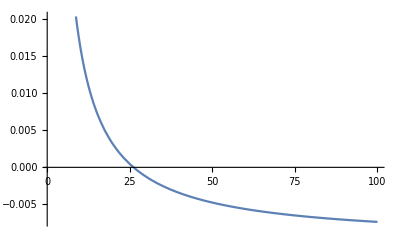

```mathematica
Plot[y[3,B, 1],{B,χ + 0.01,100}]
```

```mathematica
FindRoot[Re[y[3,B, 1]], {B,  χ + 0.01,  χ + 0.01, 100000}, MaxIterations->10000]
```

{B→26.1303}

```mathematica
CapitalCashTransferRates=Range[0.8,10,1/4]
```

{0.8,1.05,1.3,1.55,1.8,2.05,2.3,2.55,2.8,3.05,3.3,3.55,3.8,4.05,4.3,4.55,4.8,5.05,5.3,5.55,5.8,6.05,6.3,6.55,6.8,7.05,7.3,7.55,7.8,8.05,8.3,8.55,8.8,9.05,9.3,9.55,9.8}

```mathematica
sol1 := FindRoot[Re[y[1.5,B, #]], {B,  χ + 0.01,  χ + 0.01, 100000000}]&/@CapitalCashTransferRates
solutions1 = B/.sol1
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{37.0518,30.5781,26.5523,23.7973,21.7878,20.2538,19.0422,18.0595,17.2453,16.5589,15.9718,15.4635,15.0187,14.626,14.2765,13.9633,13.6808,13.4247,13.1912,12.9775,12.781,12.5998,12.4319,12.2761,12.1309,11.9953,11.8683,11.7492,11.6371,11.5315,11.4318,11.3375,11.2482,11.1634,11.0828,11.0061,10.9331}

```mathematica
sol2 := FindRoot[Re[y[2,B, #]], {B,  χ + 0.01,  χ + 0.01, 100000000}]&/@CapitalCashTransferRates
solutions2 = B/.sol2
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

{34.0726,28.334,24.7565,22.3027,20.5092,19.1374,18.052,17.1702,16.4384,15.8207,15.2915,14.8328,14.431,14.0758,13.7593,13.4754,13.2192,12.9866,12.7744,12.58,12.4012,12.236,12.083,11.9408,11.8083,11.6844,11.5684,11.4594,11.3569,11.2602,11.1688,11.0824,11.0004,10.9226,10.8487,10.7783,10.7111}

```mathematica
sol3 := FindRoot[Re[y[3,B, #]], {B,  χ + 0.01,  χ + 0.01, 100000000}]&/@CapitalCashTransferRates
solutions3 = B/.sol3
```

{30.1415,25.3593,22.366,20.3054,18.7944,17.6353,16.7156,15.9665,15.3436,14.8165,14.3641,13.9713,13.6265,13.3212,13.0489,12.8042,12.5829,12.3819,12.1983,12.0299,11.8747,11.7313,11.5983,11.4746,11.3592,11.2512,11.1499,11.0547,10.9651,10.8805,10.8006,10.7248,10.653,10.5847,10.5198,10.4579,10.3989}

```mathematica
sol4 := FindRoot[Re[y[4,B, #]], {B,  χ + 0.01,  χ + 0.01, 100000000}]&/@CapitalCashTransferRates
solutions4 = B/.sol4
```

{27.504,23.3465,20.7363,18.9346,17.6103,16.5922,15.7829,15.1227,14.5726,14.1066,13.7061,13.3579,13.0519,12.7807,12.5384,12.3206,12.1235,11.9442,11.7803,11.6298,11.4911,11.3628,11.2438,11.1329,11.0295,10.9326,10.8417,10.7563,10.6757,10.5997,10.5278,10.4596,10.3949,10.3335,10.275,10.2192,10.166}

```mathematica
(*We can also produce Figure 7 (b) directly in Mathematica but in our case, to keep the same format, we are going to export the data points and we are going to import them to R: ProbabilityofExtremePovertyAnalysisBvsct.R.*)
```

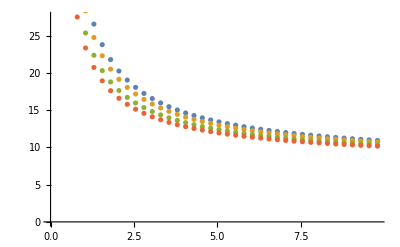

```mathematica
data1=Transpose@{CapitalCashTransferRates,solutions1};
data2=Transpose@{CapitalCashTransferRates,solutions2};
data3=Transpose@{CapitalCashTransferRates,solutions3};
data4=Transpose@{CapitalCashTransferRates,solutions4};
ListPlot[{data1,data2, data3, data4}]
```